```mathematica
Exit[]
```

```mathematica
f[x_]:=V(x*H+(1-x)e A+(1-x)(1-e) R)-2*Max[M,x V t]-Max[M, t Abs[a-(1-x)e V]]- Max[M , t(1-x)(1-e) V]-Max[M , t(1-x)e V]-Max[M,Abs[ t( b-(1-x)(1-e) V)]];
```

```mathematica
CForm[f[x]]
```

V*(A*e*(1 - x) + (1 - e)*R*(1 - x) + H*x) - 
   Max(M,(1 - e)*t*V*(1 - x)) - Max(M,e*t*V*(1 - x)) - 
   2*Max(M,t*V*x) - Max(M,Abs(t*(b - (1 - e)*V*(1 - x)))) - 
   Max(M,t*Abs(a - e*V*(1 - x)))

```mathematica
f[x_]:=V(x*H+(1-x)e A+(1-x)(1-e) R)-2*Max[M,x V t]-Max[M, t Abs[a-(1-x)e V]]- Max[M , t(1-x)(1-e) V]-Max[M , t(1-x)e V]-Max[M,Abs[ t( b-(1-x)(1-e) V)]];
S=Solve[mu==f[x],x];A1=Flatten[{#[[2]]}&/@Transpose[S][[1]]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{(-6 M-mu+A e V+R V-e R V)/((A e-H+R-e R) V),(-4 M-mu+A e V+R V-e R V)/((A e-H+R-e R+2 t) V),(-4 M-mu-a t+A e V+R V-e R V)/((A e-H+R-e R) V),(-2 M-mu-a t+A e V+R V-e R V)/((A e-H+R-e R+2 t) V),(-mu+a t+b t+A e V+R V-e R V-2 t V)/((A e-H+R-e R) V),(-4 M-mu+A e V+R V-e R V-t V)/((A e-H+R-e R-t) V),(-2 M-mu+A e V+R V-e R V-t V)/((A e-H+R-e R+t) V),(-2 M-mu+a t+A e V+R V-e R V-t V)/((A e-H+R-e R+t) V),(-2 M-mu+b t+A e V+R V-e R V-t V)/((A e-H+R-e R+t) V),(-2 M-mu+a t+b t+A e V+R V-e R V-t V)/((A e-H+R-e R+t) V),(4 M+mu-a t-A e V-R V+e R V+t V)/((-A e+H-R+e R+t) V),-(4 M+mu-b t-A e V-R V+e R V+t V)/((A e-H+R-e R-t) V),(4 M+mu-a t-b t-A e V-R V+e R V+t V)/((-A e+H-R+e R+t) V),(2 M+mu-a t-b t-A e V-R V+e R V+2 t V)/((-A e+H-R+e R+2 t) V),(-5 M-mu+A e V+R V-e R V-e t V)/((A e-H+R-e R-e t) V),(-3 M-mu+A e V+R V-e R V-e t V)/((A e-H+R-e R+2 t-e t) V),(-5 M-mu-a t+A e V+R V-e R V+e t V)/((A e-H+R-e R+e t) V),(-3 M-mu-a t+A e V+R V-e R V+e t V)/((A e-H+R-e R+2 t+e t) V),(3 M+mu-a t-A e V-R V+e R V+e t V)/((-A e+H-R+e R-2 t+e t) V),(5 M+mu-a t-A e V-R V+e R V+e t V)/((-A e+H-R+e R+e t) V),(-3 M-mu+b t+A e V+R V-e R V-2 t V+e t V)/((A e-H+R-e R-2 t+e t) V),(-M-mu+b t+A e V+R V-e R V-2 t V+e t V)/((A e-H+R-e R+e t) V),(-3 M-mu+a t+b t+A e V+R V-e R V-2 t V+e t V)/((A e-H+R-e R-2 t+e t) V),(-M-mu+a t+b t+A e V+R V-e R V-2 t V+e t V)/((A e-H+R-e R+e t) V),(-5 M-mu+A e V+R V-e R V-t V+e t V)/((A e-H+R-e R-t+e t) V),(-3 M-mu+A e V+R V-e R V-t V+e t V)/((A e-H+R-e R+t+e t) V),(-3 M-mu-a t+A e V+R V-e R V-t V+e t V)/((A e-H+R-e R-t+e t) V),(-M-mu-a t+A e V+R V-e R V-t V+e t V)/((A e-H+R-e R+t+e t) V),(-5 M-mu+b t+A e V+R V-e R V-t V+e t V)/((A e-H+R-e R-t+e t) V),(-3 M-mu+b t+A e V+R V-e R V-t V+e t V)/((A e-H+R-e R+t+e t) V),(-3 M-mu-a t+b t+A e V+R V-e R V-t V+e t V)/((A e-H+R-e R-t+e t) V),(-M-mu-a t+b t+A e V+R V-e R V-t V+e t V)/((A e-H+R-e R+t+e t) V),(M+mu-a t-A e V-R V+e R V+t V+e t V)/((-A e+H-R+e R-t+e t) V),(3 M+mu-a t-A e V-R V+e R V+t V+e t V)/((-A e+H-R+e R+t+e t) V),(M+mu-a t-b t-A e V-R V+e R V+t V+e t V)/((-A e+H-R+e R-t+e t) V),(3 M+mu-a t-b t-A e V-R V+e R V+t V+e t V)/((-A e+H-R+e R+t+e t) V),(2 M+mu-a t-A e V-R V+e R V+2 e t V)/((-A e+H-R+e R-2 t+2 e t) V),(4 M+mu-a t-A e V-R V+e R V+2 e t V)/((-A e+H-R+e R+2 e t) V),(-4 M-mu+b t+A e V+R V-e R V-2 t V+2 e t V)/((A e-H+R-e R-2 t+2 e t) V),(-2 M-mu+b t+A e V+R V-e R V-2 t V+2 e t V)/((A e-H+R-e R+2 e t) V),(-mu-a t+b t+A e V+R V-e R V-2 t V+2 e t V)/((A e-H+R-e R+2 e t) V),(-2 M-mu-a t+b t+A e V+R V-e R V-2 t V+2 e t V)/((A e-H+R-e R-2 t+2 e t) V),(-4 M-mu-a t+A e V+R V-e R V-t V+2 e t V)/((A e-H+R-e R-t+2 e t) V),(-2 M-mu-a t+A e V+R V-e R V-t V+2 e t V)/((A e-H+R-e R+t+2 e t) V),(-4 M-mu-a t+b t+A e V+R V-e R V-t V+2 e t V)/((A e-H+R-e R-t+2 e t) V),(-2 M-mu-a t+b t+A e V+R V-e R V-t V+2 e t V)/((A e-H+R-e R+t+2 e t) V),(-3 M-mu-a t+b t+A e V+R V-e R V-2 t V+3 e t V)/((A e-H+R-e R-2 t+3 e t) V),(-M-mu-a t+b t+A e V+R V-e R V-2 t V+3 e t V)/((A e-H+R-e R+3 e t) V)}

```mathematica
Union[A1,A2]
```

{(-6 M-mu+A e V+R V-e R V)/((A e-H+R-e R) V),(-4 M-mu+A e V+R V-e R V)/((A e-H+R-e R+2 t) V),(-4 M-mu-a t+A e V+R V-e R V)/((A e-H+R-e R) V),(-2 M-mu-a t+A e V+R V-e R V)/((A e-H+R-e R+2 t) V),(-4 M-mu-b t+A e V+R V-e R V)/((A e-H+R-e R) V),(-2 M-mu-b t+A e V+R V-e R V)/((A e-H+R-e R+2 t) V),(-mu-a t-b t+A e V+R V-e R V)/((A e-H+R-e R+2 t) V),(-2 M-mu-a t-b t+A e V+R V-e R V)/((A e-H+R-e R) V),(-mu+a t+b t+A e V+R V-e R V-2 t V)/((A e-H+R-e R) V),(-4 M-mu+A e V+R V-e R V-t V)/((A e-H+R-e R-t) V),(-2 M-mu+A e V+R V-e R V-t V)/((A e-H+R-e R+t) V),(-2 M-mu+a t+A e V+R V-e R V-t V)/((A e-H+R-e R+t) V),(-2 M-mu+b t+A e V+R V-e R V-t V)/((A e-H+R-e R+t) V),(-2 M-mu+a t+b t+A e V+R V-e R V-t V)/((A e-H+R-e R+t) V),(-4 M-mu-a t-b t+A e V+R V-e R V+t V)/((A e-H+R-e R+t) V),(-2 M-mu-a t-b t+A e V+R V-e R V+t V)/((A e-H+R-e R+3 t) V),(4 M+mu-a t-A e V-R V+e R V+t V)/((-A e+H-R+e R+t) V),-(4 M+mu-b t-A e V-R V+e R V+t V)/((A e-H+R-e R-t) V),(4 M+mu-a t-b t-A e V-R V+e R V+t V)/((-A e+H-R+e R+t) V),(2 M+mu-a t-b t-A e V-R V+e R V+2 t V)/((-A e+H-R+e R+2 t) V),(-5 M-mu+A e V+R V-e R V-e t V)/((A e-H+R-e R-e t) V),(-3 M-mu+A e V+R V-e R V-e t V)/((A e-H+R-e R+2 t-e t) V),(-5 M-mu-a t+A e V+R V-e R V+e t V)/((A e-H+R-e R+e t) V),(-3 M-mu-a t+A e V+R V-e R V+e t V)/((A e-H+R-e R+2 t+e t) V),(-3 M-mu-a t-b t+A e V+R V-e R V+e t V)/((A e-H+R-e R+e t) V),(-M-mu-a t-b t+A e V+R V-e R V+e t V)/((A e-H+R-e R+2 t+e t) V),(3 M+mu-a t-A e V-R V+e R V+e t V)/((-A e+H-R+e R-2 t+e t) V),(5 M+mu-a t-A e V-R V+e R V+e t V)/((-A e+H-R+e R+e t) V),-(M+mu+b t-A e V-R V+e R V+e t V)/((A e-H+R-e R+2 t-e t) V),-(3 M+mu+b t-A e V-R V+e R V+e t V)/((A e-H+R-e R-e t) V),(M+mu-a t+b t-A e V-R V+e R V+e t V)/((-A e+H-R+e R-2 t+e t) V),(3 M+mu-a t+b t-A e V-R V+e R V+e t V)/((-A e+H-R+e R+e t) V),(-3 M-mu+b t+A e V+R V-e R V-2 t V+e t V)/((A e-H+R-e R-2 t+e t) V),(-M-mu+b t+A e V+R V-e R V-2 t V+e t V)/((A e-H+R-e R+e t) V),(-3 M-mu+a t+b t+A e V+R V-e R V-2 t V+e t V)/((A e-H+R-e R-2 t+e t) V),(-M-mu+a t+b t+A e V+R V-e R V-2 t V+e t V)/((A e-H+R-e R+e t) V),(-5 M-mu+A e V+R V-e R V-t V+e t V)/((A e-H+R-e R-t+e t) V),(-3 M-mu+A e V+R V-e R V-t V+e t V)/((A e-H+R-e R+t+e t) V),(-3 M-mu-a t+A e V+R V-e R V-t V+e t V)/((A e-H+R-e R-t+e t) V),(-M-mu-a t+A e V+R V-e R V-t V+e t V)/((A e-H+R-e R+t+e t) V),(-5 M-mu+b t+A e V+R V-e R V-t V+e t V)/((A e-H+R-e R-t+e t) V),(-3 M-mu+b t+A e V+R V-e R V-t V+e t V)/((A e-H+R-e R+t+e t) V),(-3 M-mu-a t+b t+A e V+R V-e R V-t V+e t V)/((A e-H+R-e R-t+e t) V),(-M-mu-a t+b t+A e V+R V-e R V-t V+e t V)/((A e-H+R-e R+t+e t) V),-(3 M+mu+b t-A e V-R V+e R V-t V+e t V)/((A e-H+R-e R+3 t-e t) V),-(5 M+mu+b t-A e V-R V+e R V-t V+e t V)/((A e-H+R-e R+t-e t) V),(M+mu+a t+b t-A e V-R V+e R V-t V+e t V)/((-A e+H-R+e R-3 t+e t) V),(3 M+mu+a t+b t-A e V-R V+e R V-t V+e t V)/((-A e+H-R+e R-t+e t) V),(M+mu-a t-A e V-R V+e R V+t V+e t V)/((-A e+H-R+e R-t+e t) V),(3 M+mu-a t-A e V-R V+e R V+t V+e t V)/((-A e+H-R+e R+t+e t) V),(M+mu-a t-b t-A e V-R V+e R V+t V+e t V)/((-A e+H-R+e R-t+e t) V),(3 M+mu-a t-b t-A e V-R V+e R V+t V+e t V)/((-A e+H-R+e R+t+e t) V),(2 M+mu-a t-A e V-R V+e R V+2 e t V)/((-A e+H-R+e R-2 t+2 e t) V),(4 M+mu-a t-A e V-R V+e R V+2 e t V)/((-A e+H-R+e R+2 e t) V),(mu-a t+b t-A e V-R V+e R V+2 e t V)/((-A e+H-R+e R-2 t+2 e t) V),(2 M+mu-a t+b t-A e V-R V+e R V+2 e t V)/((-A e+H-R+e R+2 e t) V),(-4 M-mu+b t+A e V+R V-e R V-2 t V+2 e t V)/((A e-H+R-e R-2 t+2 e t) V),(-2 M-mu+b t+A e V+R V-e R V-2 t V+2 e t V)/((A e-H+R-e R+2 e t) V),(-mu-a t+b t+A e V+R V-e R V-2 t V+2 e t V)/((A e-H+R-e R+2 e t) V),(-2 M-mu-a t+b t+A e V+R V-e R V-2 t V+2 e t V)/((A e-H+R-e R-2 t+2 e t) V),(-4 M-mu-a t+A e V+R V-e R V-t V+2 e t V)/((A e-H+R-e R-t+2 e t) V),(-2 M-mu-a t+A e V+R V-e R V-t V+2 e t V)/((A e-H+R-e R+t+2 e t) V),(-4 M-mu-a t+b t+A e V+R V-e R V-t V+2 e t V)/((A e-H+R-e R-t+2 e t) V),(-2 M-mu-a t+b t+A e V+R V-e R V-t V+2 e t V)/((A e-H+R-e R+t+2 e t) V),-(2 M+mu+b t-A e V-R V+e R V-t V+2 e t V)/((A e-H+R-e R+3 t-2 e t) V),-(4 M+mu+b t-A e V-R V+e R V-t V+2 e t V)/((A e-H+R-e R+t-2 e t) V),(2 M+mu-a t+b t-A e V-R V+e R V-t V+2 e t V)/((-A e+H-R+e R-3 t+2 e t) V),(4 M+mu-a t+b t-A e V-R V+e R V-t V+2 e t V)/((-A e+H-R+e R-t+2 e t) V),(-3 M-mu-a t+b t+A e V+R V-e R V-2 t V+3 e t V)/((A e-H+R-e R-2 t+3 e t) V),(-M-mu-a t+b t+A e V+R V-e R V-2 t V+3 e t V)/((A e-H+R-e R+3 e t) V),(M+mu-a t+b t-A e V-R V+e R V-t V+3 e t V)/((-A e+H-R+e R-3 t+3 e t) V),(3 M+mu-a t+b t-A e V-R V+e R V-t V+3 e t V)/((-A e+H-R+e R-t+3 e t) V)}

```mathematica
Length[{(-6 M-mu+A e V+R V-e R V)/((A e-H+R-e R) V),(-4 M-mu+A e V+R V-e R V)/((A e-H+R-e R+2 t) V),(-4 M-mu-a t+A e V+R V-e R V)/((A e-H+R-e R) V),(-2 M-mu-a t+A e V+R V-e R V)/((A e-H+R-e R+2 t) V),(-4 M-mu-b t+A e V+R V-e R V)/((A e-H+R-e R) V),(-2 M-mu-b t+A e V+R V-e R V)/((A e-H+R-e R+2 t) V),(-mu-a t-b t+A e V+R V-e R V)/((A e-H+R-e R+2 t) V),(-2 M-mu-a t-b t+A e V+R V-e R V)/((A e-H+R-e R) V),(-mu+a t+b t+A e V+R V-e R V-2 t V)/((A e-H+R-e R) V),(-4 M-mu+A e V+R V-e R V-t V)/((A e-H+R-e R-t) V),(-2 M-mu+A e V+R V-e R V-t V)/((A e-H+R-e R+t) V),(-2 M-mu+a t+A e V+R V-e R V-t V)/((A e-H+R-e R+t) V),(-2 M-mu+b t+A e V+R V-e R V-t V)/((A e-H+R-e R+t) V),(-2 M-mu+a t+b t+A e V+R V-e R V-t V)/((A e-H+R-e R+t) V),(-4 M-mu-a t-b t+A e V+R V-e R V+t V)/((A e-H+R-e R+t) V),(-2 M-mu-a t-b t+A e V+R V-e R V+t V)/((A e-H+R-e R+3 t) V),(4 M+mu-a t-A e V-R V+e R V+t V)/((-A e+H-R+e R+t) V),-(4 M+mu-b t-A e V-R V+e R V+t V)/((A e-H+R-e R-t) V),(4 M+mu-a t-b t-A e V-R V+e R V+t V)/((-A e+H-R+e R+t) V),(2 M+mu-a t-b t-A e V-R V+e R V+2 t V)/((-A e+H-R+e R+2 t) V),(-5 M-mu+A e V+R V-e R V-e t V)/((A e-H+R-e R-e t) V),(-3 M-mu+A e V+R V-e R V-e t V)/((A e-H+R-e R+2 t-e t) V),(-5 M-mu-a t+A e V+R V-e R V+e t V)/((A e-H+R-e R+e t) V),(-3 M-mu-a t+A e V+R V-e R V+e t V)/((A e-H+R-e R+2 t+e t) V),(-3 M-mu-a t-b t+A e V+R V-e R V+e t V)/((A e-H+R-e R+e t) V),(-M-mu-a t-b t+A e V+R V-e R V+e t V)/((A e-H+R-e R+2 t+e t) V),(3 M+mu-a t-A e V-R V+e R V+e t V)/((-A e+H-R+e R-2 t+e t) V),(5 M+mu-a t-A e V-R V+e R V+e t V)/((-A e+H-R+e R+e t) V),-(M+mu+b t-A e V-R V+e R V+e t V)/((A e-H+R-e R+2 t-e t) V),-(3 M+mu+b t-A e V-R V+e R V+e t V)/((A e-H+R-e R-e t) V),(M+mu-a t+b t-A e V-R V+e R V+e t V)/((-A e+H-R+e R-2 t+e t) V),(3 M+mu-a t+b t-A e V-R V+e R V+e t V)/((-A e+H-R+e R+e t) V),(-3 M-mu+b t+A e V+R V-e R V-2 t V+e t V)/((A e-H+R-e R-2 t+e t) V),(-M-mu+b t+A e V+R V-e R V-2 t V+e t V)/((A e-H+R-e R+e t) V),(-3 M-mu+a t+b t+A e V+R V-e R V-2 t V+e t V)/((A e-H+R-e R-2 t+e t) V),(-M-mu+a t+b t+A e V+R V-e R V-2 t V+e t V)/((A e-H+R-e R+e t) V),(-5 M-mu+A e V+R V-e R V-t V+e t V)/((A e-H+R-e R-t+e t) V),(-3 M-mu+A e V+R V-e R V-t V+e t V)/((A e-H+R-e R+t+e t) V),(-3 M-mu-a t+A e V+R V-e R V-t V+e t V)/((A e-H+R-e R-t+e t) V),(-M-mu-a t+A e V+R V-e R V-t V+e t V)/((A e-H+R-e R+t+e t) V),(-5 M-mu+b t+A e V+R V-e R V-t V+e t V)/((A e-H+R-e R-t+e t) V),(-3 M-mu+b t+A e V+R V-e R V-t V+e t V)/((A e-H+R-e R+t+e t) V),(-3 M-mu-a t+b t+A e V+R V-e R V-t V+e t V)/((A e-H+R-e R-t+e t) V),(-M-mu-a t+b t+A e V+R V-e R V-t V+e t V)/((A e-H+R-e R+t+e t) V),-(3 M+mu+b t-A e V-R V+e R V-t V+e t V)/((A e-H+R-e R+3 t-e t) V),-(5 M+mu+b t-A e V-R V+e R V-t V+e t V)/((A e-H+R-e R+t-e t) V),(M+mu+a t+b t-A e V-R V+e R V-t V+e t V)/((-A e+H-R+e R-3 t+e t) V),(3 M+mu+a t+b t-A e V-R V+e R V-t V+e t V)/((-A e+H-R+e R-t+e t) V),(M+mu-a t-A e V-R V+e R V+t V+e t V)/((-A e+H-R+e R-t+e t) V),(3 M+mu-a t-A e V-R V+e R V+t V+e t V)/((-A e+H-R+e R+t+e t) V),(M+mu-a t-b t-A e V-R V+e R V+t V+e t V)/((-A e+H-R+e R-t+e t) V),(3 M+mu-a t-b t-A e V-R V+e R V+t V+e t V)/((-A e+H-R+e R+t+e t) V),(2 M+mu-a t-A e V-R V+e R V+2 e t V)/((-A e+H-R+e R-2 t+2 e t) V),(4 M+mu-a t-A e V-R V+e R V+2 e t V)/((-A e+H-R+e R+2 e t) V),(mu-a t+b t-A e V-R V+e R V+2 e t V)/((-A e+H-R+e R-2 t+2 e t) V),(2 M+mu-a t+b t-A e V-R V+e R V+2 e t V)/((-A e+H-R+e R+2 e t) V),(-4 M-mu+b t+A e V+R V-e R V-2 t V+2 e t V)/((A e-H+R-e R-2 t+2 e t) V),(-2 M-mu+b t+A e V+R V-e R V-2 t V+2 e t V)/((A e-H+R-e R+2 e t) V),(-mu-a t+b t+A e V+R V-e R V-2 t V+2 e t V)/((A e-H+R-e R+2 e t) V),(-2 M-mu-a t+b t+A e V+R V-e R V-2 t V+2 e t V)/((A e-H+R-e R-2 t+2 e t) V),(-4 M-mu-a t+A e V+R V-e R V-t V+2 e t V)/((A e-H+R-e R-t+2 e t) V),(-2 M-mu-a t+A e V+R V-e R V-t V+2 e t V)/((A e-H+R-e R+t+2 e t) V),(-4 M-mu-a t+b t+A e V+R V-e R V-t V+2 e t V)/((A e-H+R-e R-t+2 e t) V),(-2 M-mu-a t+b t+A e V+R V-e R V-t V+2 e t V)/((A e-H+R-e R+t+2 e t) V),-(2 M+mu+b t-A e V-R V+e R V-t V+2 e t V)/((A e-H+R-e R+3 t-2 e t) V),-(4 M+mu+b t-A e V-R V+e R V-t V+2 e t V)/((A e-H+R-e R+t-2 e t) V),(2 M+mu-a t+b t-A e V-R V+e R V-t V+2 e t V)/((-A e+H-R+e R-3 t+2 e t) V),(4 M+mu-a t+b t-A e V-R V+e R V-t V+2 e t V)/((-A e+H-R+e R-t+2 e t) V),(-3 M-mu-a t+b t+A e V+R V-e R V-2 t V+3 e t V)/((A e-H+R-e R-2 t+3 e t) V),(-M-mu-a t+b t+A e V+R V-e R V-2 t V+3 e t V)/((A e-H+R-e R+3 e t) V),(M+mu-a t+b t-A e V-R V+e R V-t V+3 e t V)/((-A e+H-R+e R-3 t+3 e t) V),(3 M+mu-a t+b t-A e V-R V+e R V-t V+3 e t V)/((-A e+H-R+e R-t+3 e t) V)}]
```

72

```mathematica
CForm[%]
```

List((-6*M - mu + A*e*V + R*V - e*R*V)/((A*e - H + R - e*R)*V),
   (-4*M - mu + A*e*V + R*V - e*R*V)/((A*e - H + R - e*R + 2*t)*V),
   (-4*M - mu - a*t + A*e*V + R*V - e*R*V)/((A*e - H + R - e*R)*V),
   (-2*M - mu - a*t + A*e*V + R*V - e*R*V)/
    ((A*e - H + R - e*R + 2*t)*V),
   (-4*M - mu - b*t + A*e*V + R*V - e*R*V)/((A*e - H + R - e*R)*V),
   (-2*M - mu - b*t + A*e*V + R*V - e*R*V)/
    ((A*e - H + R - e*R + 2*t)*V),
   (-mu - a*t - b*t + A*e*V + R*V - e*R*V)/
    ((A*e - H + R - e*R + 2*t)*V),
   (-2*M - mu - a*t - b*t + A*e*V + R*V - e*R*V)/
    ((A*e - H + R - e*R)*V),(-mu + a*t + b*t + A*e*V + R*V - e*R*V - 
      2*t*V)/((A*e - H + R - e*R)*V),
   (-4*M - mu + A*e*V + R*V - e*R*V - t*V)/((A*e - H + R - e*R - t)*V),
   (-2*M - mu + A*e*V + R*V - e*R*V - t*V)/((A*e - H + R - e*R + t)*V),
   (-2*M - mu + a*t + A*e*V + R*V - e*R*V - t*V)/
    ((A*e - H + R - e*R + t)*V),
   (-2*M - mu + b*t + A*e*V + R*V - e*R*V - t*V)/
    ((A*e - H + R - e*R + t)*V),
   (-2*M - mu + a*t + b*t + A*e*V + R*V - e*R*V - t*V)/
    ((A*e - H + R - e*R + t)*V),
   (-4*M - mu - a*t - b*t + A*e*V + R*V - e*R*V + t*V)/
    ((A*e - H + R - e*R + t)*V),
   (-2*M - mu - a*t - b*t + A*e*V + R*V - e*R*V + t*V)/
    ((A*e - H + R - e*R + 3*t)*V),
   (4*M + mu - a*t - A*e*V - R*V + e*R*V + t*V)/
    ((-(A*e) + H - R + e*R + t)*V),
   -((4*M + mu - b*t - A*e*V - R*V + e*R*V + t*V)/
      ((A*e - H + R - e*R - t)*V)),
   (4*M + mu - a*t - b*t - A*e*V - R*V + e*R*V + t*V)/
    ((-(A*e) + H - R + e*R + t)*V),
   (2*M + mu - a*t - b*t - A*e*V - R*V + e*R*V + 2*t*V)/
    ((-(A*e) + H - R + e*R + 2*t)*V),
   (-5*M - mu + A*e*V + R*V - e*R*V - e*t*V)/
    ((A*e - H + R - e*R - e*t)*V),
   (-3*M - mu + A*e*V + R*V - e*R*V - e*t*V)/
    ((A*e - H + R - e*R + 2*t - e*t)*V),
   (-5*M - mu - a*t + A*e*V + R*V - e*R*V + e*t*V)/
    ((A*e - H + R - e*R + e*t)*V),
   (-3*M - mu - a*t + A*e*V + R*V - e*R*V + e*t*V)/
    ((A*e - H + R - e*R + 2*t + e*t)*V),
   (-3*M - mu - a*t - b*t + A*e*V + R*V - e*R*V + e*t*V)/
    ((A*e - H + R - e*R + e*t)*V),
   (-M - mu - a*t - b*t + A*e*V + R*V - e*R*V + e*t*V)/
    ((A*e - H + R - e*R + 2*t + e*t)*V),
   (3*M + mu - a*t - A*e*V - R*V + e*R*V + e*t*V)/
    ((-(A*e) + H - R + e*R - 2*t + e*t)*V),
   (5*M + mu - a*t - A*e*V - R*V + e*R*V + e*t*V)/
    ((-(A*e) + H - R + e*R + e*t)*V),
   -((M + mu + b*t - A*e*V - R*V + e*R*V + e*t*V)/
      ((A*e - H + R - e*R + 2*t - e*t)*V)),
   -((3*M + mu + b*t - A*e*V - R*V + e*R*V + e*t*V)/
      ((A*e - H + R - e*R - e*t)*V)),
   (M + mu - a*t + b*t - A*e*V - R*V + e*R*V + e*t*V)/
    ((-(A*e) + H - R + e*R - 2*t + e*t)*V),
   (3*M + mu - a*t + b*t - A*e*V - R*V + e*R*V + e*t*V)/
    ((-(A*e) + H - R + e*R + e*t)*V),
   (-3*M - mu + b*t + A*e*V + R*V - e*R*V - 2*t*V + e*t*V)/
    ((A*e - H + R - e*R - 2*t + e*t)*V),
   (-M - mu + b*t + A*e*V + R*V - e*R*V - 2*t*V + e*t*V)/
    ((A*e - H + R - e*R + e*t)*V),
   (-3*M - mu + a*t + b*t + A*e*V + R*V - e*R*V - 2*t*V + e*t*V)/
    ((A*e - H + R - e*R - 2*t + e*t)*V),
   (-M - mu + a*t + b*t + A*e*V + R*V - e*R*V - 2*t*V + e*t*V)/
    ((A*e - H + R - e*R + e*t)*V),
   (-5*M - mu + A*e*V + R*V - e*R*V - t*V + e*t*V)/
    ((A*e - H + R - e*R - t + e*t)*V),
   (-3*M - mu + A*e*V + R*V - e*R*V - t*V + e*t*V)/
    ((A*e - H + R - e*R + t + e*t)*V),
   (-3*M - mu - a*t + A*e*V + R*V - e*R*V - t*V + e*t*V)/
    ((A*e - H + R - e*R - t + e*t)*V),
   (-M - mu - a*t + A*e*V + R*V - e*R*V - t*V + e*t*V)/
    ((A*e - H + R - e*R + t + e*t)*V),
   (-5*M - mu + b*t + A*e*V + R*V - e*R*V - t*V + e*t*V)/
    ((A*e - H + R - e*R - t + e*t)*V),
   (-3*M - mu + b*t + A*e*V + R*V - e*R*V - t*V + e*t*V)/
    ((A*e - H + R - e*R + t + e*t)*V),
   (-3*M - mu - a*t + b*t + A*e*V + R*V - e*R*V - t*V + e*t*V)/
    ((A*e - H + R - e*R - t + e*t)*V),
   (-M - mu - a*t + b*t + A*e*V + R*V - e*R*V - t*V + e*t*V)/
    ((A*e - H + R - e*R + t + e*t)*V),
   -((3*M + mu + b*t - A*e*V - R*V + e*R*V - t*V + e*t*V)/
      ((A*e - H + R - e*R + 3*t - e*t)*V)),
   -((5*M + mu + b*t - A*e*V - R*V + e*R*V - t*V + e*t*V)/
      ((A*e - H + R - e*R + t - e*t)*V)),
   (M + mu + a*t + b*t - A*e*V - R*V + e*R*V - t*V + e*t*V)/
    ((-(A*e) + H - R + e*R - 3*t + e*t)*V),
   (3*M + mu + a*t + b*t - A*e*V - R*V + e*R*V - t*V + e*t*V)/
    ((-(A*e) + H - R + e*R - t + e*t)*V),
   (M + mu - a*t - A*e*V - R*V + e*R*V + t*V + e*t*V)/
    ((-(A*e) + H - R + e*R - t + e*t)*V),
   (3*M + mu - a*t - A*e*V - R*V + e*R*V + t*V + e*t*V)/
    ((-(A*e) + H - R + e*R + t + e*t)*V),
   (M + mu - a*t - b*t - A*e*V - R*V + e*R*V + t*V + e*t*V)/
    ((-(A*e) + H - R + e*R - t + e*t)*V),
   (3*M + mu - a*t - b*t - A*e*V - R*V + e*R*V + t*V + e*t*V)/
    ((-(A*e) + H - R + e*R + t + e*t)*V),
   (2*M + mu - a*t - A*e*V - R*V + e*R*V + 2*e*t*V)/
    ((-(A*e) + H - R + e*R - 2*t + 2*e*t)*V),
   (4*M + mu - a*t - A*e*V - R*V + e*R*V + 2*e*t*V)/
    ((-(A*e) + H - R + e*R + 2*e*t)*V),
   (mu - a*t + b*t - A*e*V - R*V + e*R*V + 2*e*t*V)/
    ((-(A*e) + H - R + e*R - 2*t + 2*e*t)*V),
   (2*M + mu - a*t + b*t - A*e*V - R*V + e*R*V + 2*e*t*V)/
    ((-(A*e) + H - R + e*R + 2*e*t)*V),
   (-4*M - mu + b*t + A*e*V + R*V - e*R*V - 2*t*V + 2*e*t*V)/
    ((A*e - H + R - e*R - 2*t + 2*e*t)*V),
   (-2*M - mu + b*t + A*e*V + R*V - e*R*V - 2*t*V + 2*e*t*V)/
    ((A*e - H + R - e*R + 2*e*t)*V),
   (-mu - a*t + b*t + A*e*V + R*V - e*R*V - 2*t*V + 2*e*t*V)/
    ((A*e - H + R - e*R + 2*e*t)*V),
   (-2*M - mu - a*t + b*t + A*e*V + R*V - e*R*V - 2*t*V + 2*e*t*V)/
    ((A*e - H + R - e*R - 2*t + 2*e*t)*V),
   (-4*M - mu - a*t + A*e*V + R*V - e*R*V - t*V + 2*e*t*V)/
    ((A*e - H + R - e*R - t + 2*e*t)*V),
   (-2*M - mu - a*t + A*e*V + R*V - e*R*V - t*V + 2*e*t*V)/
    ((A*e - H + R - e*R + t + 2*e*t)*V),
   (-4*M - mu - a*t + b*t + A*e*V + R*V - e*R*V - t*V + 2*e*t*V)/
    ((A*e - H + R - e*R - t + 2*e*t)*V),
   (-2*M - mu - a*t + b*t + A*e*V + R*V - e*R*V - t*V + 2*e*t*V)/
    ((A*e - H + R - e*R + t + 2*e*t)*V),
   -((2*M + mu + b*t - A*e*V - R*V + e*R*V - t*V + 2*e*t*V)/
      ((A*e - H + R - e*R + 3*t - 2*e*t)*V)),
   -((4*M + mu + b*t - A*e*V - R*V + e*R*V - t*V + 2*e*t*V)/
      ((A*e - H + R - e*R + t - 2*e*t)*V)),
   (2*M + mu - a*t + b*t - A*e*V - R*V + e*R*V - t*V + 2*e*t*V)/
    ((-(A*e) + H - R + e*R - 3*t + 2*e*t)*V),
   (4*M + mu - a*t + b*t - A*e*V - R*V + e*R*V - t*V + 2*e*t*V)/
    ((-(A*e) + H - R + e*R - t + 2*e*t)*V),
   (-3*M - mu - a*t + b*t + A*e*V + R*V - e*R*V - 2*t*V + 3*e*t*V)/
    ((A*e - H + R - e*R - 2*t + 3*e*t)*V),
   (-M - mu - a*t + b*t + A*e*V + R*V - e*R*V - 2*t*V + 3*e*t*V)/
    ((A*e - H + R - e*R + 3*e*t)*V),
   (M + mu - a*t + b*t - A*e*V - R*V + e*R*V - t*V + 3*e*t*V)/
    ((-(A*e) + H - R + e*R - 3*t + 3*e*t)*V),
   (3*M + mu - a*t + b*t - A*e*V - R*V + e*R*V - t*V + 3*e*t*V)/
    ((-(A*e) + H - R + e*R - t + 3*e*t)*V))

```mathematica
mu=-32;H=3;A=1.1;R=10.10;a=5;b=3;c=0.1;e=0.9;M=10;G=8;t=9;
f[x_]:=(a+b+c)(x*H+(1-x)e A+(1-x)(1-e) R)-3 G-Min[M,x (a+b+c)t]-Min[M, t Abs[a-(1-x)e (a+b+c)]]- Min[M , Abs[t (b-(1-x)(1-e) (a+b+c))]];
```

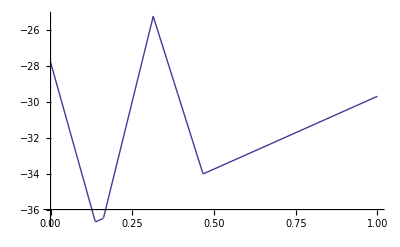

```mathematica
Plot[f[x],{x,0.0,1},PlotRange->All]
```

```mathematica
Solve[f[x]==mu]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0.0648148},{x→0.222629},{x→0.431403},{x→0.716049}}